```mathematica
url="https://raw.githubusercontent.com/dnaneet/ML/master/se/data.dat";
datasetDirty=Import[url, "Data"];
(*names={'celcius','bar','region','kJPerKg'}*)
dataset=Select[datasetDirty, #[[3]]≠ 0&]; (*Select only those rows and columns with non zero region*)
s=Dimensions[dataset][[1]];T=dataset[[2;;s,1]]; (*temperature, C*)
P=dataset[[2;;s,2]]; (*pressure, bar*)
r=dataset[[2;;s,3]]/.{0->"r0",1->"r1", 2->"r2", 3->"r3", 4->"r4", 5->"r5"}; (*region, class/label*)
h=dataset[[2;;s,4]];
```

```mathematica
subset3d=Thread[{P,T,h}];
c3d=FindClusters[subset3d,4];
```

```mathematica
ListPlot3D[{c3d[[1]],c3d[[2]],c3d[[3]],c3d[[4]]},ImageSize->Large,Mesh->None]
```

-Graphics3D-

#### Zone 1

```mathematica
z=1;
t1=Table[c3d[[z]][[i]][[1]],{i,1,Dimensions[c3d[[z]]][[1]],1}];
p1=Table[c3d[[z]][[i]][[2]],{i,1,Dimensions[c3d[[z]]][[1]],1}];
h1=Table[c3d[[z]][[i]][[3]],{i,1,Dimensions[c3d[[z]]][[1]],1}];
dz1=Length[zone1]
```

9596

```mathematica
SeedRandom[123];
zone1=
Thread[
RandomSample[Table[
{t1[[i]],p1[[i]]}->{h1[[i]]},{i,1,Dimensions[t1][[1]],1}]]
];
```

```mathematica
zone1Training=zone1[[1;;Ceiling[0.95*dz1]]];
Length[zone1Training]
```

9117

```mathematica
net=NetChain[{
64,Tanh,32,8,1},
"Input"->2]
nnz1=NetTrain[net,zone1]
```

NetChain[<>]

NetChain[<>]

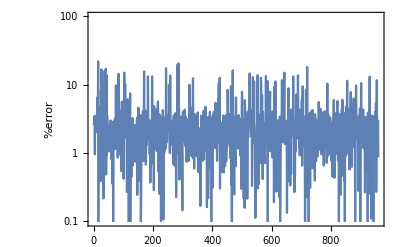

11.4283

```mathematica
e1=Flatten[
Table[(nnz1[zone1[[i]][[1]]]-zone1[[i,2]])*100/zone1[[i,2]],{i,1,Dimensions[t1][[1]],10}]];
ListLogPlot[Abs[e1],Joined->True,Frame->True,FrameStyle->Black,FrameLabel->{"","%error"},PlotRange->{All,{0,100}}]
Max[e1]
```

#### Zone 2

```mathematica
z=2;
t2=Table[c3d[[z]][[i]][[1]],{i,1,Dimensions[c3d[[z]]][[1]],1}];
p2=Table[c3d[[z]][[i]][[2]],{i,1,Dimensions[c3d[[z]]][[1]],1}];
h2=Table[c3d[[z]][[i]][[3]],{i,1,Dimensions[c3d[[z]]][[1]],1}];
dz2=Length[t2]
```

10776

```mathematica
zone2=
Thread[
RandomSample[
Table[
{t2[[i]],p2[[i]]}->{h2[[i]]},{i,1,Dimensions[t2][[1]],1}]
]
];
```

```mathematica
zone2Training=zone2[[1;;Ceiling[0.95*dz2]]];
Length[zone2Training]
```

10238

```mathematica
nnz2=NetTrain[net,zone2Training]
```

NetChain[<>]

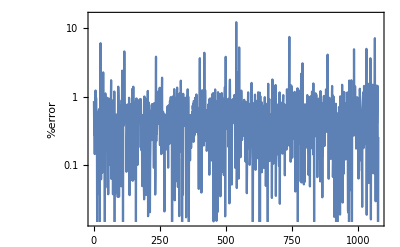

12.3574

```mathematica
e2=Flatten[
Table[(nnz2[zone2[[i]][[1]]]-zone2[[i,2]])*100/zone2[[i,2]],{i,1,Dimensions[t2][[1]],10}]];
ListLogPlot[Abs[e2],Joined->True,Frame->True,FrameStyle->Black,FrameLabel->{"","%error"},PlotRange->{All,{0,15}}]
Max[e2]
```

#### Zone 3

```mathematica
z=3;
t3=Table[c3d[[z]][[i]][[1]],{i,1,Dimensions[c3d[[z]]][[1]],1}];
p3=Table[c3d[[z]][[i]][[2]],{i,1,Dimensions[c3d[[z]]][[1]],1}];
h3=Table[c3d[[z]][[i]][[3]],{i,1,Dimensions[c3d[[z]]][[1]],1}];
dz3=Length[t3]
```

3842

```mathematica
zone3=
Thread[
RandomSample[
Table[
{t3[[i]],p3[[i]]}->{h3[[i]]},{i,1,Dimensions[t3][[1]],1}]
]
];
zone3Training=zone3[[1;;Ceiling[0.95*dz3]]];
Length[zone3Training]
```

3650

```mathematica
nnz3=NetTrain[net,zone3Training]
```

NetChain[<>]

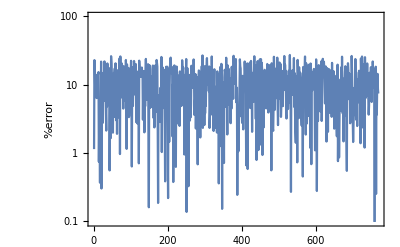

27.2574

```mathematica
e3=Flatten[
Table[(nnz3[zone3[[i]][[1]]]-zone3[[i,2]])*100/zone3[[i,2]],{i,1,Dimensions[t3][[1]],5}]];
ListLogPlot[Abs[e3],Joined->True,Frame->True,FrameStyle->Black,FrameLabel->{"","%error"},PlotRange->{All,{0,100}}]
Max[e3]
```

#### Zone 4

```mathematica
z=4;
t4=Table[c3d[[z]][[i]][[1]],{i,1,Dimensions[c3d[[z]]][[1]],1}];
p4=Table[c3d[[z]][[i]][[2]],{i,1,Dimensions[c3d[[z]]][[1]],1}];
h4=Table[c3d[[z]][[i]][[3]],{i,1,Dimensions[c3d[[z]]][[1]],1}];
dz4=Length[t4]
```

12365

```mathematica
zone4=
Thread[
RandomSample[
Table[
{t4[[i]],p4[[i]]}->{h4[[i]]},{i,1,Dimensions[t4][[1]],1}]
]
];
zone4Training=zone4[[1;;Ceiling[0.95*dz4]]];
Length[zone4Training]
```

11747

```mathematica
nnz4=NetTrain[net,zone4Training]
```

NetChain[<>]

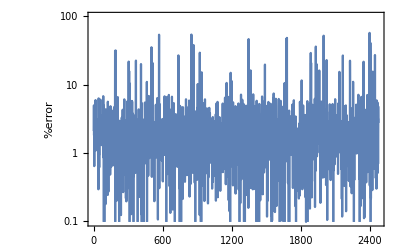

57.4842

```mathematica
e4=Flatten[
Table[(nnz4[zone4[[i]][[1]]]-zone4[[i,2]])*100/zone4[[i,2]],{i,1,Dimensions[t4][[1]],5}]];
ListLogPlot[Abs[e4],Joined->True,Frame->True,FrameStyle->Black,FrameLabel->{"","%error"},PlotRange->{All,{0,100}}]
Max[e4]
```

#### All data

```mathematica
allData=Join[zone1, zone2, zone3, zone4];
lAll=Length[allData]
```

36579

```mathematica
allDataTraining=RandomSample[allData[[1;;Ceiling[0.95*lAll]]]];
```

```mathematica
nnAll=NetTrain[net,allDataTraining]
```

NetChain[<>]

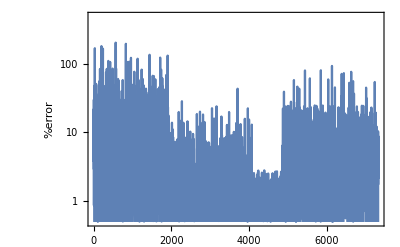

206.701

```mathematica
eAll=Flatten[
Table[(nnAll[allData[[i]][[1]]]-allData[[i,2]])*100/allData[[i,2]],{i,1,lAll,5}]];
ListLogPlot[Abs[eAll],Joined->True,Frame->True,FrameStyle->Black,FrameLabel->{"","%error"},PlotRange->{All,{0,500}}]
Max[eAll]
```

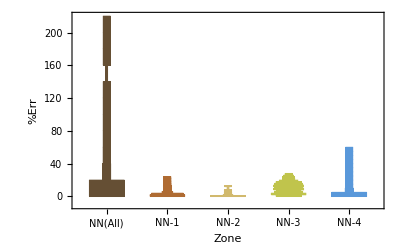

```mathematica
zones={e1,e2,e3,e4,eAll};
DistributionChart[Abs[{eAll, e1, e2, e3, e4}],ChartStyle->"SouthwestColors", ChartElementFunction->"HistogramDensity",Frame->True,FrameStyle->Black,FrameLabel->{"Zone","%Err"},ChartLabels->{"NN(All)","NN-1","NN-2","NN-3","NN-4"},
ChartLabels->Placed[{zones,Length/@zones},{Axis,Center}]]
```

```mathematica
ListPlot3D[{c3d[[1]],c3d[[2]],c3d[[3]],c3d[[4]]},PlotLegends->{"Zone-1", "Zone-2", "Zone-3", "Zone-4"},Mesh->None,InterpolationOrder->1]
```

-Graphics3D-